```mathematica
Лабораторная работа №6 Ковальчук В.В. ПО-4
```

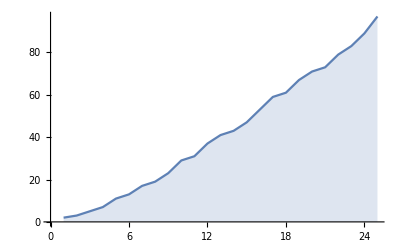

```mathematica
ListLinePlot[Prime[Range[25]],Filling->Axis]
```

```mathematica
data1=RandomVariate[NormalDistribution[0,1],500];
data2=RandomVariate[NormalDistribution[3,1/2],500];
```

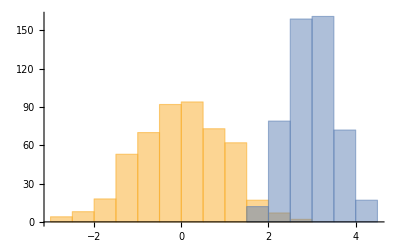

```mathematica
Histogram[{data1,data2}]
```

```mathematica
ListPlot3D[{{1,1,1,1},{1,2,1,2},{1,1,3,1},{1,2,1,4}},Mesh->All]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[Sin[j^2+i],{i,0,3,0.1},{j,0,3,0.1}]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[Sin[j^2+i],{i,0,3,0.2},{j,0,3,0.2}], Filling -> Bottom, ColorFunction->"Rainbow"]
```

-Graphics3D-

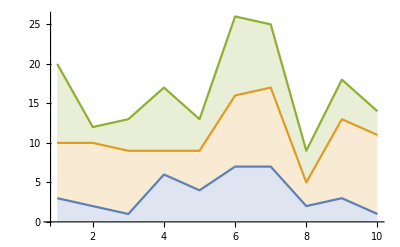

```mathematica
StackedListPlot[{{3,2,1,6,4,7,7,2,3,1},{7,8,8,3,5,9,10,3,10,10},{10,2,4,8,4,10,8,4,5,3}}]
```

```mathematica
Fit[{2,3,5,7,11,13},{1,x,x^2},x]
```

0.9+0.689286 x+0.232143 x^2

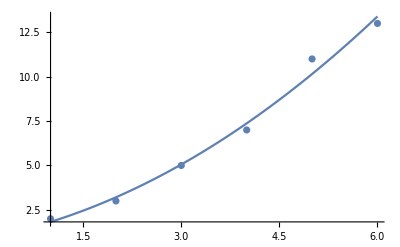

```mathematica
Show[{Plot[%,{x,1,6}],ListPlot[{2,3,5,7,11,13}]}]
```

```mathematica
image = Import["C:\\Users\\User\\Desktop\\pictures\\donut.png"]
```

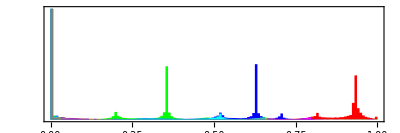

```mathematica
ImageHistogram[image]
```

```mathematica
Row[image, Erosion[image, DiskMatrix[7]]]
```

Row[-Graphics-,-Graphics-]

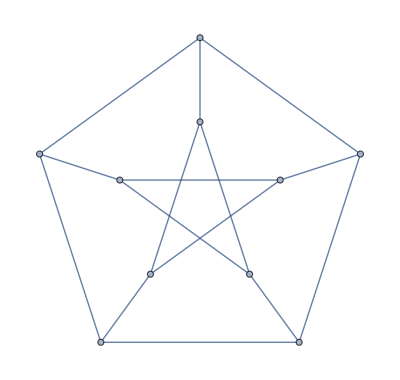

```mathematica
GraphPlot[PetersenGraph[]]
```

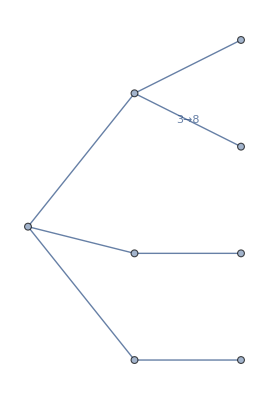

```mathematica
TreePlot[{1->4,1->6,1->8,2->6,{3->8,"3→8"},4->5,7->8},Left]
```

```mathematica
WolframAlpha["2+5"]
```

WolframAlphaQueryResults

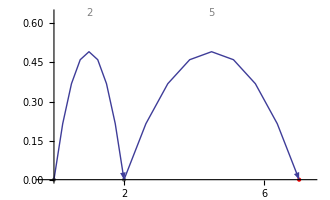
{2+5,7,-Graphics-,seven,-Graphics- | + | -Graphics- | == | -Graphics-
2 |  | 5 |  | 7,  age 6: 4.2 seconds  |    age 8: 2.2 seconds  |    age 10: 1.4 seconds  |    
age 18: 0.88 seconds
(ignoring concentration, repetition, variations in education, etc.)}

```mathematica
WolframAlpha["2+5","PodCells"]
```

```mathematica
WolframAlpha["2+5","Image"]
```

-Graphics-

```mathematica
WolframAlpha["2+5","SpokenResult"]
```

2 plus 5 is 7

```mathematica
WolframAlpha["2+5","ShortAnswer"]
```

7

```mathematica
WolframAlpha["population of Belarus",{{"Result",1},"Plaintext"}]
```

9.45 million people (world rank: 96th) (2020 estimate)

```mathematica
WolframAlpha["population of europe countries",{{"Result", 1}, "Plaintext"}]
```

total | 750 million people
highest | 146 million people (Russia)
lowest | 809 people (Vatican City) | (2013, 2014, 2017, and 2020 estimates)